```mathematica
getParaxial[ni_,nf_]:=nf/ni
getDerWavefront[ni_,nf_]:=-ni/(nf (-1+√((nf^2-ni^2)/nf^2)))
getLeastConfusion[na_,ni_,nf_,dcs_]:=-(x/.NSolve[-((((dcs na)/(√(1-na^2/nf^2) nf)+(na ni x)/(nf^2 √(1-(na^2 ni^2)/nf^4)))√(nf^2-ni^2))/(dcs nf))^(2/3)+((-ni x)/(dcs nf))^(2/3)==1,x][[1]])/dcs
```

```mathematica
getϵmin[nr_]:=-(-140 nr-42 nr^3-42 nr^5-15 nr^7)/(140+84 nr^2+15 nr^4)
```

```mathematica
getWmin[nr_]:=-(-3 π (√(-1+nr^2)+nr^2 ArcCsc[nr])+8 (nr+nr^3) EllipticE[1/nr^2]-8 nr (-1+nr^2) EllipticK[1/nr^2])/(2 (1-9 nr^2+6 nr^2 √(-1+nr^2) ArcCsc[nr]+3 nr^4 ArcCsc[nr]^2))
getWminapprox[nr_]:=(nr^3 (37+170 nr^2))/(7+60 nr^2+140 nr^4)
```

# Derivation of criteria for best focus

Define the wavefront error and its approximation up to fourth order

```mathematica
abeW[u_,nr_,α_]:=1/nr √(1-( nr u)^2)+ α √(1-u^2)
approxW[u_,nr_,α_]:=1/nr+α-1/2(nr+α)u^2-1/8(nr^3+α)u^4
```

```mathematica
Series[abeW[u,nr,α],{u,0,4}]
```

(1/nr+α)+(-nr/2-α/2) u^2+(-nr^3/8-α/8) u^4+O[u]^5

#### Paraxial (second order W rms)

```mathematica
getParaxial[nr_]:=nr
```

#### Fourth order W rms

```mathematica
Clear[nr]
```

Note that the nr multiplying the terms is there because the definition is with u running from 0 to 1 (the SA).

```mathematica
approxWmean[α_,nr_]=Assuming[{nr>1,α∈Reals},Integrate[nr^2 approxW[u,nr,α]u,{u,0,1/nr},{f,0,2π}]/π]
approxW2mean[α_,nr_] =Assuming[{α∈Reals},Integrate[nr^2(approxW[u,nr,α] )^2 u ,{u,0,1/nr},{f,0,2π}]/π]
```

((17 π)/(24 nr)+π α-(π α)/(24 nr^4)-(π α)/(4 nr^2))/π

((171 π)/(320 nr^2)-(11 π α)/(240 nr^5)-(29 π α)/(96 nr^3)+(17 π α)/(12 nr)+π α^2+(π α^2)/(320 nr^8)+(π α^2)/(32 nr^6)-(π α^2)/(2 nr^2))/π

```mathematica
Assuming[{nr>1,α∈Reals},D[( approxW2mean[α,nr]-approxWmean[α,nr]^2),α]//Simplify]
```

(19 nr^3+75 nr^5+4 α+30 nr^2 α+60 nr^4 α)/(1440 nr^8)

```mathematica
Solve[(19 nr^3+75 nr^5+4 α+30 nr^2 α+60 nr^4 α)/(1440 nr^8)==0,α]
```

{{α→-(nr^3 (19+75 nr^2))/(2 (2+15 nr^2+30 nr^4))}}

```mathematica
getWminapprox[nr_]:=(nr^3 (19+75 nr^2))/(2 (2+15 nr^2+30 nr^4))
```

#### Whole W rms

```mathematica
Wmean[α_,nr_]=Assuming[{nr>1,α∈Reals},Integrate[nr^2 abeW[u,nr,α]u,{u,0,1/nr},{f,0,2π}]/π]
W2mean[α_,nr_] =Assuming[{α∈Reals},Integrate[nr^2(abeW[u,nr,α])^2 u ,{u,0,1/nr},{f,0,2π}]/π]
```

(2 (1+nr^3 α-(-1+nr^2)^(3/2) α))/(3 nr)

ConditionalExpression[(1+α (nr+nr^3-α+2 nr^2 α)-(-1+nr^2)^2 α ArcCoth[nr])/(2 nr^2), Re[nr]>1&&Im[nr]==0]

```mathematica
Assuming[{nr>1,α∈Reals},D[( W2mean[α,nr]-Wmean[α,nr]^2),α]//Simplify]
```

-1/(18 nr^2)(16 (nr^3-(-1+nr^2)^(3/2)) (1+nr^3 α-(-1+nr^2)^(3/2) α)+9 (-nr-nr^3+2 α-4 nr^2 α+(-1+nr^2)^2 ArcCoth[nr]))

```mathematica
Solve[1/(18 nr^2)(16 (nr^3-(-1+nr^2)^(3/2)) (1+nr^3 α-(-1+nr^2)^(3/2) α)+9 (-nr-nr^3+2 α-4 nr^2 α+(-1+nr^2)^2 ArcCoth[nr]))==0,α]//Simplify
```

{{α→(9 nr-7 nr^3-16 √(-1+nr^2)+16 nr^2 √(-1+nr^2)-9 (-1+nr^2)^2 ArcCoth[nr])/(2+12 nr^2-48 nr^4+32 nr^6+32 nr^3 √(-1+nr^2)-32 nr^5 √(-1+nr^2))}}

```mathematica
getWmin[nr_]:=(-9 nr+7 nr^3+16 √(-1+nr^2)-16 nr^2 √(-1+nr^2)+9 (-1+nr^2)^2 ArcCoth[nr])/(2+12 nr^2-48 nr^4+32 nr^6+32 nr^3 √(-1+nr^2)-32 nr^5 √(-1+nr^2))
```

#### Min spot size 4th order

```mathematica
ϵx[u_,ϕ_,α_,nr_]=D[approxW[u,nr,α]/.u->(√(ux^2+uy^2)),ux]/.ux->u Cos[ϕ]/.uy->u Sin[ϕ]//Simplify
```

-1/2 u (2 nr+nr^3 u^2+(2+u^2) α) Cos[ϕ]

```mathematica
Assuming[{nr>1,α∈Reals},Integrate[nr^2 ϵx [u,f,α,nr]u,{u,0,1/nr},{f,0,2π}]/π]
```

0

```mathematica
Assuming[{nr>1,α∈Reals},Integrate[nr^2 (ϵx [u,f,α,nr])^2 u,{u,0,1/nr},{f,0,2π}]/π]
```

(43 nr^6+22 nr^3 α+64 nr^5 α+3 α^2+16 nr^2 α^2+24 nr^4 α^2)/(96 nr^6)

```mathematica
Assuming[{nr>1,α∈Reals},D[((43 nr^6+22 nr^3 α+64 nr^5 α+3 α^2+16 nr^2 α^2+24 nr^4 α^2)/(96 nr^6)),α]//Simplify]
```

(11 nr^3+32 nr^5+3 α+16 nr^2 α+24 nr^4 α)/(48 nr^6)

```mathematica
Solve[(11 nr^3+32 nr^5+3 α+16 nr^2 α+24 nr^4 α)/(48 nr^6)==0,α]
```

{{α→-(nr^3 (11+32 nr^2))/(3+16 nr^2+24 nr^4)}}

```mathematica
getϵminapprox[nr_]:=(nr^3 (11+32 nr^2))/(3+16 nr^2+24 nr^4)
```

#### Min spot size whole

```mathematica
ϵx[u_,ϕ_,α_,nr_]=D[abeW[u,nr,α]/.u->(√(ux^2+uy^2)),ux]/.ux->u Cos[ϕ]/.uy->u Sin[ϕ]//Simplify
```

u (-nr/(√(1-nr^2 u^2))-α/(√(1-u^2))) Cos[ϕ]

```mathematica
D[abeW[u,nr,α]/.u->(√(ux^2+uy^2)),ux]
```

-(nr ux)/(√(1-nr^2 (ux^2+uy^2)))-(ux α)/(√(1-ux^2-uy^2))

```mathematica
Assuming[{nr>1,α∈Reals},Integrate[nr^2 ϵx [u,f,α,nr]u,{u,0,1/nr},{f,0,2π}]/π]
```

0

```mathematica
Assuming[{α∈Reals},Integrate[nr^2(abeW[u,nr,α])^2 u ,{u,0,1/nr},{f,0,2π}]/π]
```

```mathematica
D[(ϵx [u,f,α,nr])^2,α]//Simplify
```

(2 u^2 ((nr √(1-u^2))/(√(1-nr^2 u^2))+α) Cos[f]^2)/(1-u^2)

```mathematica
Assuming[{nr>1,α∈Reals},Integrate[nr^2 D[(ϵx [u,f,α,nr])^2,α]u,{u,0,1/nr},{f,0,2π}]/π]
```

-nr+(1+nr^2) ArcCosh[nr/(√(-1+nr^2))]-α (1+nr^2 Log[1-1/nr^2])

```mathematica
Solve[-nr+(1+nr^2) ArcCosh[nr/(√(-1+nr^2))]-α (1+nr^2 Log[1-1/nr^2])==0,α]
```

{{α→(nr-ArcCosh[nr/(√(-1+nr^2))]-nr^2 ArcCosh[nr/(√(-1+nr^2))])/(-1-nr^2 Log[1-1/nr^2])}}

```mathematica
(-nr+ArcCosh[nr/(√(-1+nr^2))]+nr^2 ArcCosh[nr/(√(-1+nr^2))])/(-1-nr^2 Log[1-1/nr^2])//Simplify
```

(nr-(1+nr^2) ArcCosh[nr/(√(-1+nr^2))])/(1+nr^2 Log[1-1/nr^2])

```mathematica
getϵmin[nr_]:=(nr-(1+nr^2) ArcCosh[nr/(√(-1+nr^2))])/(1+nr^2 Log[1-1/nr^2])
```

#### Confusion

```mathematica
getLeastConfusion[na_,ni_,nf_,dcs_]:=-(x/.NSolve[-((((dcs na)/(√(1-na^2/nf^2) nf)+(na ni x)/(nf^2 √(1-(na^2 ni^2)/nf^4)))√(nf^2-ni^2))/(dcs nf))^(2/3)+((-ni x)/(dcs nf))^(2/3)==1,x][[1]])/dcs
```

```mathematica
a[θ_,ni_,nf_]:=(ni Sin[θ]/nf)/(√(1-(ni Sin[θ]/nf)^2))
b[θ_,ni_,nf_,d_]:=d Tan[θ]
r[ϕ_,θ_,ni_,nf_,d_]:=b[θ,ni,nf,d]/(Sin[ϕ]-a[θ,ni,nf]Cos[ϕ])
y[x_,θ_,ni_,nf_,d_]:=a[θ,ni,nf]x+b[θ,ni,nf,d]
```

### Comparisson

```mathematica
With[{nr = 1.518/1.33},
{getParaxial[nr],getWminapprox[nr],getWmin[nr],getϵminapprox[nr],getϵmin[nr]}]
```

{1.14135,1.19748,1.40017,1.21316,2.20573}

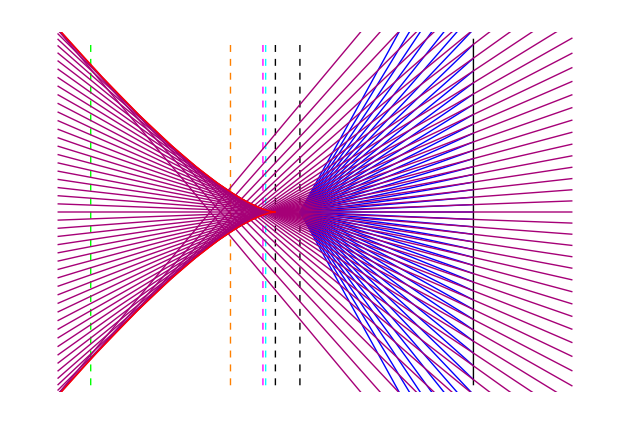

```mathematica
With[{nf=1.518,ni=1.33,na =1.33 (*1.49*),dcs=50,numθ=25,α=2.},
Block[{nr,pry=1*dcs,θimax,θilist,θflist,αnp,αpar,αϵapprox,αϵ,prxm,prxp,αlc,αWmin,αWminapprox},
nr = nf/ni;
prxm=-(.1+α)nf dcs/ni;
prxp=-(1.5-α)nf dcs/ni;
θimax=ArcSin[na/nf];
θilist=Join[Table[θ,{θ,-θimax,-θimax/numθ,θimax/numθ}],Table[θ,{θ,θimax/numθ,θimax,θimax/numθ}]];
θflist=ArcSin[ni/nf Sin[#]]&/@θilist;
(*αlc =getLeastConfusion[na,ni,nf,dcs];*)
αpar=getParaxial[nr];
αϵapprox=getϵminapprox[nf/ni];
αWminapprox=getWminapprox[nf/ni];
αϵ=getϵmin[nf/ni];
αWmin=getWmin[nf/ni];
Show[{
Graphics[{
{{Thick,Line[{{0,-pry},{0,pry}}]},
Dashed,Line[{{-dcs,-pry},{-dcs,pry}}],
Line[{{-αpar dcs,-pry},{-αpar dcs,pry}}],(*Line[{{-αderW dcs,-pry},{-αderW dcs,pry}}],*)
(*Line[{{-αlc dcs,-pry},{-αlc dcs,pry}}],*)
Magenta, Line[{{-αϵapprox dcs,-pry},{-αϵapprox dcs,pry}}],
Green,Line[{{-αϵ dcs,-pry},{-αϵ dcs,pry}}],
Orange,Line[{{-αWmin dcs,-pry},{-αWmin dcs,pry}}],
Cyan,Line[{{-αWminapprox dcs,-pry},{-αWminapprox dcs,pry}}]},{Blue,Thin,Line[{{-dcs,0},{0,0}}],Line[{{-dcs,0},{0,dcs Tan[#]}}]&/@θilist},
{Hue[0.88,1.,0.65], Thin, Line[{{prxm,0},{prxp,0}}],Line[{{prxm,y[prxm,#,ni,nf,dcs]},{prxp,y[prxp,#,ni,nf,dcs]}}]&/@θilist}}
],
ParametricPlot[{(-dcs nf)/ni Cosh[θ]^3,(dcs nf)/(√(nf^2-ni^2))Sinh[θ]^3},{θ,-π/2,π/2},PlotStyle->{Red,Thick}]}
,PlotRange->{{prxm,prxp},{-pry,pry}}]
]]
```